## RGB to LMSR This document computes a 4x3 matrix to convert linear RGB data in the Rec.709 color gamut to LMSR space. The data used in this notebook is from http://www.cvrl.org/.

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
```

## 2-deg XYZ CMFs transformed from the CIE 2006 2-deg LMS cone fundamentals

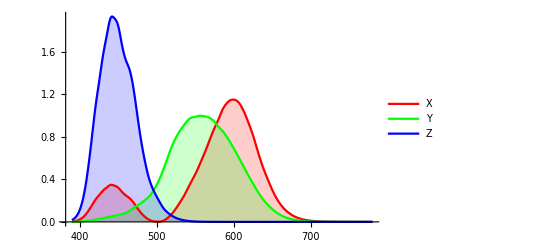

```mathematica
{λ,x,y,z}=Import["data/lin2012xyz2e_1_7sf.csv"]ᵀ;
ListLinePlot[{{λ,x}ᵀ,{λ,y}ᵀ,{λ,z}ᵀ},PlotLegends->{"X","Y","Z"},Filling->Axis,PlotStyle->{Red,Green,Blue}]
```

## 2-deg fundamentals based on the Stiles & Burch 10-deg CMFs (adjusted to 2-deg) Rods (R) response from CIE “physiologically-relevant” luminous efficiency functions consistent with the Stockman & Sharpe cone fundamentals.

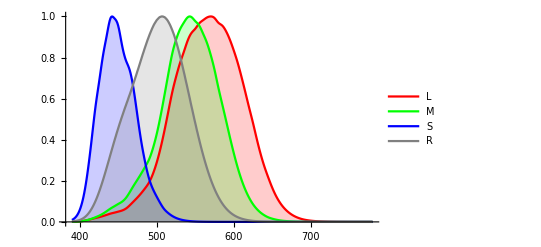

```mathematica
{λ,l,m,s}=Import["data/linss2_10e_1.csv"]ᵀ;
{λ,r}=Import["data/scvle_1.csv"]ᵀ;
ListLinePlot[{{λ,l}ᵀ,{λ,m}ᵀ,{λ,s}ᵀ,{λ,r}ᵀ},PlotLegends->{"L","M","S", "R"},Filling->Axis,PlotStyle->{Red,Green,Blue,Gray}]
```

## RGB (Rec.709) spectral reflectance Data provided by Scott Burns (http://scottburns.us/fast-rgb-to-spectrum-conversion-for-reflectances/).

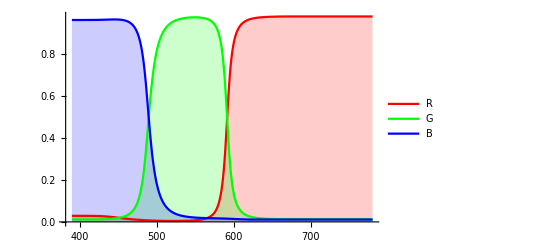

```mathematica
{λ,cr,cb,cg}=Import["data/rec709.csv"]ᵀ;
ListLinePlot[{{λ,cr}ᵀ,{λ,cb}ᵀ,{λ,cg}ᵀ},PlotLegends->{"R","G","B"},Filling->Axis,PlotStyle->{Red,Green,Blue}]
```

## CIE Illuminant D65 spectral reflectance

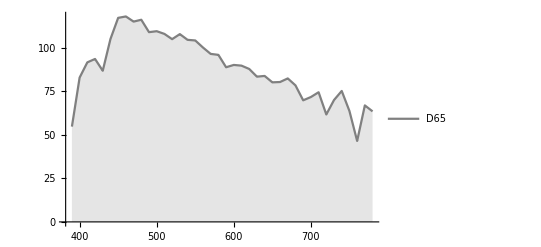

```mathematica
{λ,d65}=Import["data/d65.csv"]ᵀ;
ListLinePlot[{{λ,d65}ᵀ},PlotLegends->{"D65"},Filling->Axis,PlotStyle->{Gray}]
```

## RGB to LMSR

```mathematica
cieIlluminant=NIntegrate[Interpolation[d65][λ]*Interpolation[m][λ],{λ,1,391}];
```

```mathematica
d65ReflectanceF=Interpolation[d65/cieIlluminant];
rgbReflectanceF=Interpolation/@{cr,cb,cg};
lmsrResponseF=Interpolation/@{l,m,s,r};
```

```mathematica
rgbToLms[channel_,receptor_]:=NIntegrate[d65ReflectanceF[λ]*rgbReflectanceF[[channel]][λ]*lmsrResponseF[[receptor]][λ],{λ,1,391}];
```

### 4x3 matrix for RGB to LMSR conversion

```mathematica
rgbToLmsr=Outer[rgbToLms,{1,2,3},{1,2,3,4}]
```

{{0.310652,0.0963524,0.0121654,0.0188013},{0.768899,0.775177,0.0551166,0.635776},{0.0881365,0.12847,0.574046,0.426157}}

```mathematica
rgbToLmsr//MatrixForm
```

(0.310652 | 0.0963524 | 0.0121654 | 0.0188013
0.768899 | 0.775177 | 0.0551166 | 0.635776
0.0881365 | 0.12847 | 0.574046 | 0.426157)

```mathematica
rgbToLmsrᵀ//MatrixForm
```

(0.310652 | 0.768899 | 0.0881365
0.0963524 | 0.775177 | 0.12847
0.0121654 | 0.0551166 | 0.574046
0.0188013 | 0.635776 | 0.426157)